# Formulación de y para datos experimentales y para función dieléctrica de tipo Drude

## Para una dada

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

### Datos experimentales

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

```mathematica
mieCoefAn[np_,nm_,a_,λ_,n_]:=Module[{m,x,an},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefBn[np_,nm_,a_,λ_,n_]:=Module[{m,x,bn},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
mieQsca[np_,nm_,a_,λ_,nmax_]:=Module[{an,bn,k,Csca,Qsca},
an=mieCoefAn[np,nm,a,λ,Table[n,{n,nmax}]];
bn=mieCoefBn[np,nm,a,λ,Table[n,{n,nmax}]];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*(Sum[(2 n +1)(Norm[an[[n]] ]^2+Norm[bn[[n]]] ^2),{n,nmax}]);
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
mieQext[np_,nm_,a_,λ_,nmax_]:=Module[{an,bn,Cext,Qext},
an=mieCoefAn[np,nm,a,λ,Table[n,{n,nmax}]];
bn=mieCoefBn[np,nm,a,λ,Table[n,{n,nmax}]];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* Sum[(2 n +1)Re[an[[n]] + bn[[n]] ],{n,nmax}];
Qext=Cext/(Pi* a^2) ;{an,bn,Cext,Qext}]
```

### Modelo de Drude

```mathematica
ϵ[λ_,λp_,γ_]:=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))(*recibe λ en nm*)
```

```mathematica
ϵmieCoefAn[nm_,a_,λ_,n_,λp_,γ_]:=Module[{np,m,x,an},
						np=Sqrt[1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
ϵmieCoefBn[nm_,a_,λ_,n_,λp_,γ_]:=Module[{np,m,x,bn},
						np=Sqrt[1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
ϵmieQsca[nm_,a_,λ_,nmax_,λp_,γ_]:=Module[{an,bn,k,Csca,Qsca},
an=ϵmieCoefAn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
bn=ϵmieCoefBn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*(Sum[(2 n +1)(Norm[an[[n]] ]^2+Norm[bn[[n]]] ^2),{n,nmax}]);
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
ϵmieQext[nm_,a_,λ_,nmax_,λp_,γ_]:=Module[{an,bn,Cext,Qext},
an=ϵmieCoefAn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
bn=ϵmieCoefBn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* Sum[(2 n +1)Re[an[[n]] + bn[[n]] ],{n,nmax}];
Qext=Cext/(Pi* a^2) ;
{an,bn,Cext,Qext}]
```

## Cálculos

### Modelo de Drude

#### Para ℏω = 4.3 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
qextDrude15=Table[{(h c)/λ,ϵmieQext[1.33,30,λ,15,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}];
qscaDrude15=Table[{(h c)/λ,ϵmieQsca[1.33,30,λ,15,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}];
```

```mathematica
q2extDrude15=Table[{λ,ϵmieQext[1.33,30,λ,15,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}];
q2scaDrude15=Table[{λ,ϵmieQsca[1.33,30,λ,15,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}];
```

```mathematica
q3=Reverse[q2extDrude15];
q4=Reverse[q2scaDrude15];
```

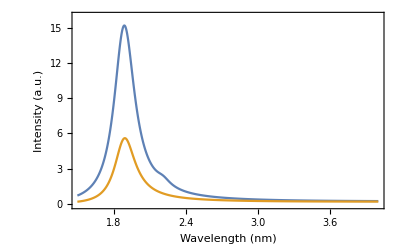

```mathematica
eVticks=Join[{h c/#,Null}&/@FindDivisions[h c/{##},8*6],{h c/#,NumberForm[N@#,4]}&/@FindDivisions[h c/{##},10]]&;
ListLinePlot[{qextDrude15,qscaDrude15},Frame->True,PlotRange->{{1.5,4},{-0.1,16}},FrameLabel->{"Wavelength (nm)","Intensity (a.u.)","Energy (eV)"},FrameTicks->{{Automatic,Automatic},{Automatic,eVticks}}]
```

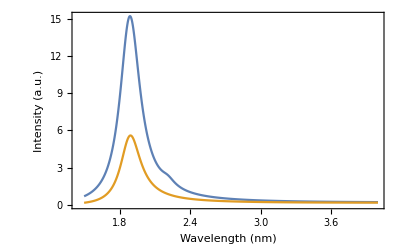

```mathematica
p1=ListLinePlot[{qextDrude15,qscaDrude15},Frame->True,FrameStyle->Directive[Black,FontFamily->"CMU Sans Serif",10],FrameLabel->{"Wavelength (nm)","Intensity (a.u.)","Energy (eV)"},PlotRange->All]
```

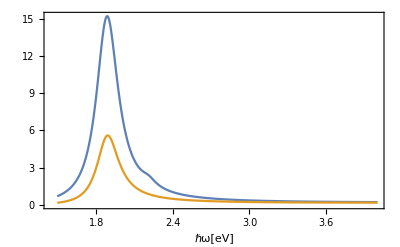

```mathematica
p1=ListLinePlot[{qextDrude15,qscaDrude15},Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->"CMU Sans Serif",10],FrameLabel->{{Style["",12],None},{Style["ℏω[eV]",12],None}},PlotRange->All]
```

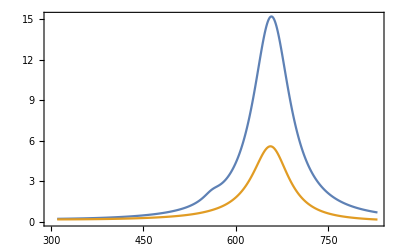

```mathematica
p2=ListLinePlot[{q3,q4},Frame->{False,False,True,True},FrameStyle->Directive[Black,FontFamily->"CMU Sans Serif",10],Ticks->{{},{2,4,6,8,10}},FrameTicks->{None,None,All,All},FrameLabel->{{None,Style["",12]},{None,Style["ℏω[eV]",12]}},PlotRange->All]
```

#### Para ℏω = 10 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
result1=Table[{(h c)/λ,ϵmieQext[1.33,30,λ,10,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}];
```

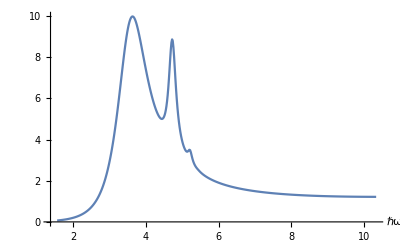

```mathematica
ListLinePlot[result1,AxesLabel->{"ℏω",""},PlotRange->All]
```

#### Para ℏω = 13.142 eV, ℏγ = 0.197 eV y a = 60 nm

```mathematica
result1=Table[{λ,ϵmieQext[1.33,60,λ,10,2 Pi c/(13.142/ℏ),0.197/ℏ][[4]]},{λ,0.5,500}];
```

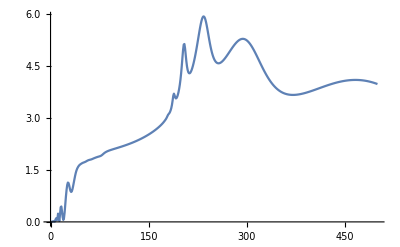

```mathematica
ListLinePlot[result1,AxesLabel->{"",""},PlotRange->All]
```

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
varindep1=Table[{(h c)/λ,mieQext[nindexalum[λ],1,10,λ,10][[3]]},{λ,1,20}];
```

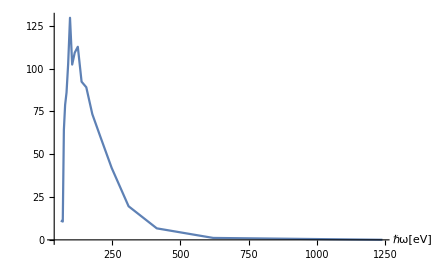

```mathematica
ListLinePlot[varindep1,AxesLabel->{"ℏω[eV]",""},PlotRange->All]
```

#### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en nm*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
aU=Transpose[{λAu,nAu}];
```

```mathematica
nindexau=Interpolation[aU];
```

```mathematica
varindep1=Table[{(h c)/λ,mieQext[nindexau[λ],1,10,λ,10][[3]]},{λ,188,1937}];
```

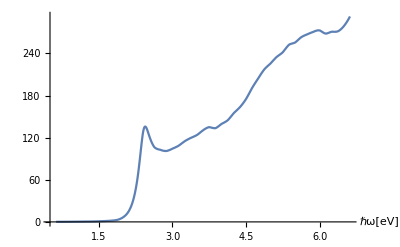

```mathematica
ListLinePlot[varindep1,AxesLabel->{"ℏω[eV]",""},PlotRange->All]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

```mathematica
varindepQextAg=Table[{(h c)/λ,mieQext[nindexplata[λ],1,10,λ,10][[3]]},{λ,188,1937}];
```

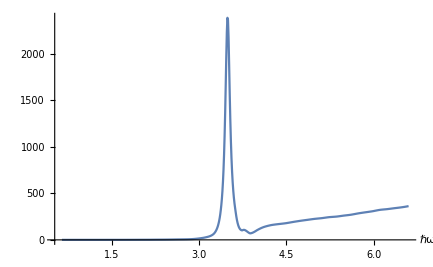

```mathematica
ListLinePlot[varindepQextAg,AxesLabel->{"ℏω",""},PlotRange->All]
```

## Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
varindepBismuto=Table[{(h c)/λ,mieQext[nindexbismuto[λ],1,10,λ,10][[3]]},{λ,2.48*10^(-3),619.9}];
```

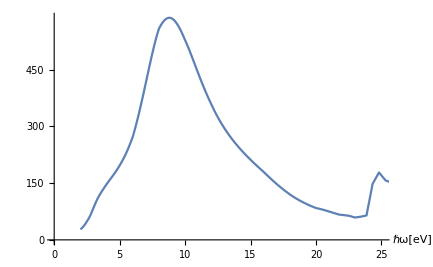

```mathematica
ListLinePlot[varindepBismuto,AxesLabel->{"ℏω[eV]",""}]
```

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

```mathematica
varindepQextMgO=Table[{(h c)/λ,mieQext[nindexMgO[λ],1,10,λ,10][[3]]},{λ,360,5400}];
```

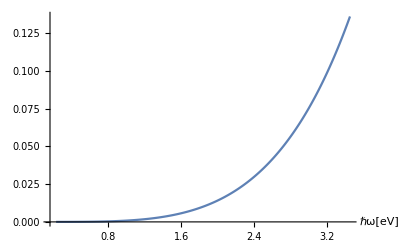

```mathematica
ListLinePlot[varindepQextMgO,AxesLabel->{"ℏω[eV]",""},PlotRange->All]
```

## Para un n fija

## Definiciones

### Datos experimentales

```mathematica
nmieQsca[np_,nm_,a_,λ_,n_]:=Module[{an,bn,k,Csca,Qsca},
an=mieCoefAn[np,nm,a,λ,n];
bn=mieCoefBn[np,nm,a,λ,n];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
nmieQext[np_,nm_,a_,λ_,n_]:=Module[{an,bn,Cext,Qext},
an=mieCoefAn[np,nm,a,λ,n];
bn=mieCoefBn[np,nm,a,λ,n];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* ((2 n +1)Re[an + bn]);
Qext=Cext/(Pi* a^2) ;{an,bn,Cext,Qext}]
```

### Modelo de Drude

```mathematica
nϵmieQsca[nm_,a_,λ_,n_,λp_,γ_]:=Module[{an,bn,k,Csca,Qsca,anCsca,anQsca},
an=ϵmieCoefAn[nm,a,λ,n,λp,γ];
bn=ϵmieCoefBn[nm,a,λ,n,λp,γ];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2+Norm[bn] ^2));

anCsca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2));
Qsca=Csca/(Pi* a^2) ;
anQsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca,anCsca,anQsca}]
```

```mathematica
nϵmieQext[nm_,a_,λ_,n_,λp_,γ_]:=Module[{an,bn,Cext,Qext,anCext,anQext},
an=ϵmieCoefAn[nm,a,λ,n,λp,γ];
bn=ϵmieCoefBn[nm,a,λ,n,λp,γ];
Cext =(λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)Re[an+ bn]);
anCext =(λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)Re[an+ bn]);
Qext=Cext/(Pi* a^2) ;
anQext=anCext/(Pi* a^2);
{an,bn,Cext,Qext,anCext,anQext}]
```

## Cálculos

### Modelo de Drude

#### Para ℏω = 4.3 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
result123=Table[{(h c)/λ,nϵmieQext[1.33,30,λ,#,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}]&/@{1,2,3};
```

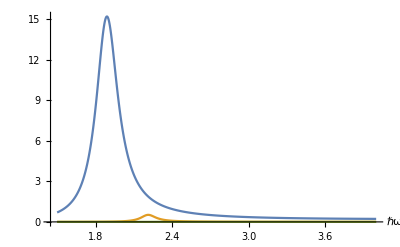

```mathematica
ListLinePlot[result123,AxesLabel->{"ℏω",""},PlotRange->All]
```

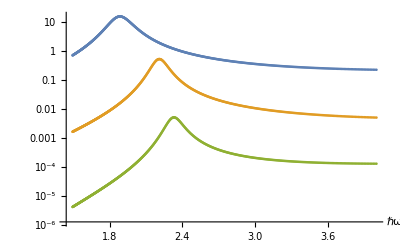

```mathematica
ListLogPlot[result123,AxesLabel->{"ℏω",""},PlotRange->All]
```

#### Para ℏω = 10 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
result1=Table[{(h c)/λ,nϵmieQext[1.33,30,λ,#,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}]&/@{1,2,3};
```

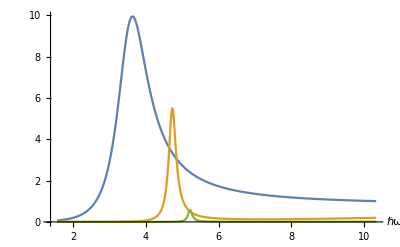

```mathematica
ListLinePlot[result1,AxesLabel->{"ℏω",""},PlotRange->All]
```

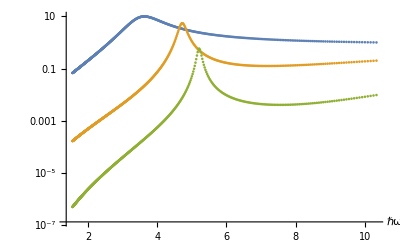

```mathematica
ListLogPlot[result1,AxesLabel->{"ℏω",""},PlotRange->All]
```

#### Para ℏω = 13.142 eV, ℏγ = 0.197 eV y a = 60 nm

```mathematica
result1=Table[{λ,nϵmieQext[1,60,λ,#,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]]},{λ,0.5,500}]&/@{1,2,3,4};
```

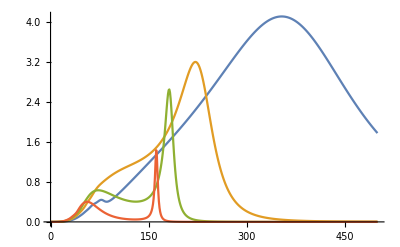

```mathematica
ListLinePlot[result1,AxesLabel->{"",""},PlotRange->All]
```